```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lackey/Research/Poisson/Testprograms

```mathematica
R[θ_, ϕ_]:=1.2*^6*(1-0.8*Cos[θ]^2)
plot0=SphericalPlot3D[R[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->1]
```

-Graphics3D-

```mathematica
H[r_, θ_, ϕ_]:=2.8*^14*(1.2*^6*(1-0.8*Cos[θ]^2)-r)
Plot[{H[r, 0, 0], H[r, 0.5, 0], H[r, π/2, 0]}, {r, 0, 2*^6}]
```

-Graphics-

```mathematica
Roftpdata=Import["surfaceoftp.txt", "Data"]
```

{{0.,0.,240000.},{0.,0.523599,240000.},{0.,1.0472,240000.},{0.,1.5708,240000.},{0.,2.0944,240000.},{0.,2.61799,240000.},{0.,3.14159,240000.},{0.,3.66519,240000.},{0.,4.18879,240000.},{0.,4.71239,240000.},{0.,5.23599,240000.},{0.,5.75959,240000.},{0.523599,0.,480000.},{0.523599,0.523599,480000.},{0.523599,1.0472,480000.},{0.523599,1.5708,480000.},{0.523599,2.0944,480000.},{0.523599,2.61799,480000.},{0.523599,3.14159,480000.},{0.523599,3.66519,480000.},{0.523599,4.18879,480000.},{0.523599,4.71239,480000.},{0.523599,5.23599,480000.},{0.523599,5.75959,480000.},{1.0472,0.,960000.},{1.0472,0.523599,960000.},{1.0472,1.0472,960000.},{1.0472,1.5708,960000.},{1.0472,2.0944,960000.},{1.0472,2.61799,960000.},{1.0472,3.14159,960000.},{1.0472,3.66519,960000.},{1.0472,4.18879,960000.},{1.0472,4.71239,960000.},{1.0472,5.23599,960000.},{1.0472,5.75959,960000.},{1.5708,0.,1.2×10^6},{1.5708,0.523599,1.2×10^6},{1.5708,1.0472,1.2×10^6},{1.5708,1.5708,1.2×10^6},{1.5708,2.0944,1.2×10^6},{1.5708,2.61799,1.2×10^6},{1.5708,3.14159,1.2×10^6},{1.5708,3.66519,1.2×10^6},{1.5708,4.18879,1.2×10^6},{1.5708,4.71239,1.2×10^6},{1.5708,5.23599,1.2×10^6},{1.5708,5.75959,1.2×10^6},{2.0944,0.,960000.},{2.0944,0.523599,960000.},{2.0944,1.0472,960000.},{2.0944,1.5708,960000.},{2.0944,2.0944,960000.},{2.0944,2.61799,960000.},{2.0944,3.14159,960000.},{2.0944,3.66519,960000.},{2.0944,4.18879,960000.},{2.0944,4.71239,960000.},{2.0944,5.23599,960000.},{2.0944,5.75959,960000.},{2.61799,0.,480000.},{2.61799,0.523599,480000.},{2.61799,1.0472,480000.},{2.61799,1.5708,480000.},{2.61799,2.0944,480000.},{2.61799,2.61799,480000.},{2.61799,3.14159,480000.},{2.61799,3.66519,480000.},{2.61799,4.18879,480000.},{2.61799,4.71239,480000.},{2.61799,5.23599,480000.},{2.61799,5.75959,480000.},{3.14159,0.,240000.},{3.14159,0.523599,240000.},{3.14159,1.0472,240000.},{3.14159,1.5708,240000.},{3.14159,2.0944,240000.},{3.14159,2.61799,240000.},{3.14159,3.14159,240000.},{3.14159,3.66519,240000.},{3.14159,4.18879,240000.},{3.14159,4.71239,240000.},{3.14159,5.23599,240000.},{3.14159,5.75959,240000.}}

```mathematica
gridlist=Table[{Roftpdata⟦i, 3⟧*Sin[Roftpdata⟦i, 1⟧]*Cos[Roftpdata⟦i, 2⟧], Roftpdata⟦i, 3⟧*Sin[Roftpdata⟦i, 1⟧]*Sin[Roftpdata⟦i, 2⟧], Roftpdata⟦i, 3⟧*Cos[Roftpdata⟦i, 1⟧]}, {i, Length[Roftpdata]}]
```

{{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{0.,0.,240000.},{240000.,0.,415692.},{207846.,120000.,415692.},{120000.,207846.,415692.},{1.46958×10^-11,240000.,415692.},{-120000.,207846.,415692.},{-207846.,120000.,415692.},{-240000.,2.93915×10^-11,415692.},{-207846.,-120000.,415692.},{-120000.,-207846.,415692.},{-4.40873×10^-11,-240000.,415692.},{120000.,-207846.,415692.},{207846.,-120000.,415692.},{831384.,0.,480000.},{720000.,415692.,480000.},{415692.,720000.,480000.},{5.09076×10^-11,831384.,480000.},{-415692.,720000.,480000.},{-720000.,415692.,480000.},{-831384.,1.01815×10^-10,480000.},{-720000.,-415692.,480000.},{-415692.,-720000.,480000.},{-1.52723×10^-10,-831384.,480000.},{415692.,-720000.,480000.},{720000.,-415692.,480000.},{1.2×10^6,0.,7.34788×10^-11},{1.03923×10^6,600000.,7.34788×10^-11},{600000.,1.03923×10^6,7.34788×10^-11},{7.34788×10^-11,1.2×10^6,7.34788×10^-11},{-600000.,1.03923×10^6,7.34788×10^-11},{-1.03923×10^6,600000.,7.34788×10^-11},{-1.2×10^6,1.46958×10^-10,7.34788×10^-11},{-1.03923×10^6,-600000.,7.34788×10^-11},{-600000.,-1.03923×10^6,7.34788×10^-11},{-2.20436×10^-10,-1.2×10^6,7.34788×10^-11},{600000.,-1.03923×10^6,7.34788×10^-11},{1.03923×10^6,-600000.,7.34788×10^-11},{831384.,0.,-480000.},{720000.,415692.,-480000.},{415692.,720000.,-480000.},{5.09076×10^-11,831384.,-480000.},{-415692.,720000.,-480000.},{-720000.,415692.,-480000.},{-831384.,1.01815×10^-10,-480000.},{-720000.,-415692.,-480000.},{-415692.,-720000.,-480000.},{-1.52723×10^-10,-831384.,-480000.},{415692.,-720000.,-480000.},{720000.,-415692.,-480000.},{240000.,0.,-415692.},{207846.,120000.,-415692.},{120000.,207846.,-415692.},{1.46958×10^-11,240000.,-415692.},{-120000.,207846.,-415692.},{-207846.,120000.,-415692.},{-240000.,2.93915×10^-11,-415692.},{-207846.,-120000.,-415692.},{-120000.,-207846.,-415692.},{-4.40873×10^-11,-240000.,-415692.},{120000.,-207846.,-415692.},{207846.,-120000.,-415692.},{2.93915×10^-11,0.,-240000.},{2.54538×10^-11,1.46958×10^-11,-240000.},{1.46958×10^-11,2.54538×10^-11,-240000.},{1.79971×10^-27,2.93915×10^-11,-240000.},{-1.46958×10^-11,2.54538×10^-11,-240000.},{-2.54538×10^-11,1.46958×10^-11,-240000.},{-2.93915×10^-11,3.59942×10^-27,-240000.},{-2.54538×10^-11,-1.46958×10^-11,-240000.},{-1.46958×10^-11,-2.54538×10^-11,-240000.},{-5.39914×10^-27,-2.93915×10^-11,-240000.},{1.46958×10^-11,-2.54538×10^-11,-240000.},{2.54538×10^-11,-1.46958×10^-11,-240000.}}

```mathematica
plot1=ListPointPlot3D[gridlist]
```

-Graphics3D-

```mathematica
Show[plot0, plot1]
```

-Graphics3D-

```mathematica
difference=Table[{Roftpdata⟦i, 1⟧,Roftpdata⟦i, 2⟧, Roftpdata⟦i, 3⟧, (Roftpdata⟦i, 3⟧-R[Roftpdata⟦i, 1⟧, Roftpdata⟦i, 2⟧])/R[Roftpdata⟦i, 1⟧, Roftpdata⟦i, 2⟧]}, {i, Length[Roftpdata]}]
```

{{0.,0.,240000.,0.},{0.,0.523599,240000.,0.},{0.,1.0472,240000.,0.},{0.,1.5708,240000.,0.},{0.,2.0944,240000.,0.},{0.,2.61799,240000.,0.},{0.,3.14159,240000.,0.},{0.,3.66519,240000.,0.},{0.,4.18879,240000.,0.},{0.,4.71239,240000.,0.},{0.,5.23599,240000.,0.},{0.,5.75959,240000.,0.},{0.523599,0.,480000.,1.21266×10^-16},{0.523599,0.523599,480000.,1.21266×10^-16},{0.523599,1.0472,480000.,1.21266×10^-16},{0.523599,1.5708,480000.,1.21266×10^-16},{0.523599,2.0944,480000.,1.21266×10^-16},{0.523599,2.61799,480000.,1.21266×10^-16},{0.523599,3.14159,480000.,1.21266×10^-16},{0.523599,3.66519,480000.,1.21266×10^-16},{0.523599,4.18879,480000.,1.21266×10^-16},{0.523599,4.71239,480000.,1.21266×10^-16},{0.523599,5.23599,480000.,1.21266×10^-16},{0.523599,5.75959,480000.,1.21266×10^-16},{1.0472,0.,960000.,-1.21266×10^-16},{1.0472,0.523599,960000.,-1.21266×10^-16},{1.0472,1.0472,960000.,-1.21266×10^-16},{1.0472,1.5708,960000.,-1.21266×10^-16},{1.0472,2.0944,960000.,-1.21266×10^-16},{1.0472,2.61799,960000.,-1.21266×10^-16},{1.0472,3.14159,960000.,-1.21266×10^-16},{1.0472,3.66519,960000.,-1.21266×10^-16},{1.0472,4.18879,960000.,-1.21266×10^-16},{1.0472,4.71239,960000.,-1.21266×10^-16},{1.0472,5.23599,960000.,-1.21266×10^-16},{1.0472,5.75959,960000.,-1.21266×10^-16},{1.5708,0.,1.2×10^6,0.},{1.5708,0.523599,1.2×10^6,0.},{1.5708,1.0472,1.2×10^6,0.},{1.5708,1.5708,1.2×10^6,0.},{1.5708,2.0944,1.2×10^6,0.},{1.5708,2.61799,1.2×10^6,0.},{1.5708,3.14159,1.2×10^6,0.},{1.5708,3.66519,1.2×10^6,0.},{1.5708,4.18879,1.2×10^6,0.},{1.5708,4.71239,1.2×10^6,0.},{1.5708,5.23599,1.2×10^6,0.},{1.5708,5.75959,1.2×10^6,0.},{2.0944,0.,960000.,0.},{2.0944,0.523599,960000.,0.},{2.0944,1.0472,960000.,0.},{2.0944,1.5708,960000.,0.},{2.0944,2.0944,960000.,0.},{2.0944,2.61799,960000.,0.},{2.0944,3.14159,960000.,0.},{2.0944,3.66519,960000.,0.},{2.0944,4.18879,960000.,0.},{2.0944,4.71239,960000.,0.},{2.0944,5.23599,960000.,0.},{2.0944,5.75959,960000.,0.},{2.61799,0.,480000.,1.21266×10^-16},{2.61799,0.523599,480000.,1.21266×10^-16},{2.61799,1.0472,480000.,1.21266×10^-16},{2.61799,1.5708,480000.,1.21266×10^-16},{2.61799,2.0944,480000.,1.21266×10^-16},{2.61799,2.61799,480000.,1.21266×10^-16},{2.61799,3.14159,480000.,1.21266×10^-16},{2.61799,3.66519,480000.,1.21266×10^-16},{2.61799,4.18879,480000.,1.21266×10^-16},{2.61799,4.71239,480000.,1.21266×10^-16},{2.61799,5.23599,480000.,1.21266×10^-16},{2.61799,5.75959,480000.,1.21266×10^-16},{3.14159,0.,240000.,0.},{3.14159,0.523599,240000.,0.},{3.14159,1.0472,240000.,0.},{3.14159,1.5708,240000.,0.},{3.14159,2.0944,240000.,0.},{3.14159,2.61799,240000.,0.},{3.14159,3.14159,240000.,0.},{3.14159,3.66519,240000.,0.},{3.14159,4.18879,240000.,0.},{3.14159,4.71239,240000.,0.},{3.14159,5.23599,240000.,0.},{3.14159,5.75959,240000.,0.}}

```mathematica
Max[difference⟦All, {4}⟧]
```

1.21266×10^-16

```mathematica
R2[θ_, ϕ_]:=(1+0.3*LegendreP[2, Cos[θ]]+0.4*LegendreP[3, Cos[θ]])*(1+0.02Cos[8ϕ])
SphericalPlot3D[R2[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->1]
```

-Graphics3D-

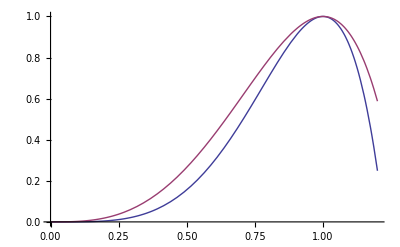

```mathematica
A0[ξ_]:=3*ξ^4-2*ξ^6
B0[ξ_]:=1/2(5*ξ^3-3*ξ^5)
Plot[{A0[ξ], B0[ξ]}, {ξ, 0, 1.2}]
```

```mathematica
Roots[A0[ξ]==0, ξ]
Roots[B0[ξ]==0, ξ]
```

ξ==0||ξ==0||ξ==0||ξ==0||ξ==√(3/2)||ξ==-√(3/2)

ξ==0||ξ==0||ξ==0||ξ==√(5/3)||ξ==-√(5/3)

```mathematica
(*Roots[A0[ξ]==a, ξ]
Roots[B0[ξ]==b, ξ]*)
```

```mathematica
r0[ξ_, α_, f_, g_]:=α*(ξ+A0[ξ]*f+B0[ξ]*g)
```

```mathematica
(*Roots[r0[ξ, α, f, g]==0, ξ]*)
```

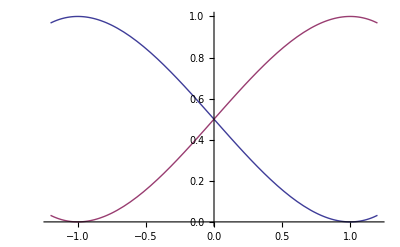

```mathematica
A[ξ_]:=1/4(ξ^3-3*ξ+2)
B[ξ_]:=1/4(-ξ^3+3*ξ+2)
Plot[{A[ξ], B[ξ]}, {ξ, -1.2, 1.2}]
```

```mathematica
Roots[A[ξ]==0, ξ]
Roots[B[ξ]==0, ξ]
```

ξ==-2||ξ==1||ξ==1

ξ==-1||ξ==-1||ξ==2

```mathematica
r[ξ_, α_, β_, f_, g_]:=α*(ξ+1/4(ξ^3-3*ξ+2)*f+1/4(-ξ^3+3*ξ+2)*g)+β
```

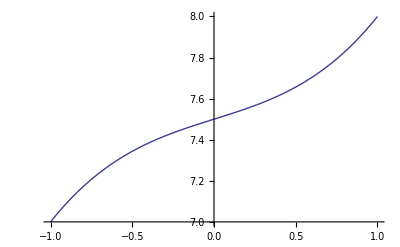

```mathematica
Plot[r[ξ, 1, 5, 3, 2], {ξ, -1, 1}]
```

```mathematica
FindRoot[r[ξ, 1, 5, 3, 2]==7.2, {ξ, 0}]
```

{ξ→-0.760375}

```mathematica
-0.7603745901723008
```

```mathematica
(*Roots[r[ξ, α, β, f, g]==0, ξ]*)
```

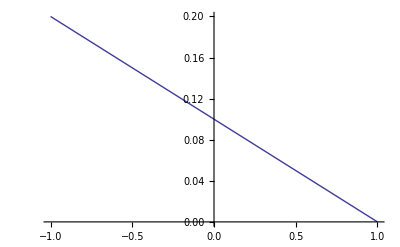

```mathematica
u[ξ_, α_, f_]:=α*(ξ+1/4(ξ^3-3*ξ+2)*f-1)
Plot[u[ξ, -0.1, 0], {ξ, -1, 1}]
```

```mathematica
FindRoot[u[ξ, -0.1, 0]==1/5.0, {ξ, 0}]
```

{ξ→-1.}

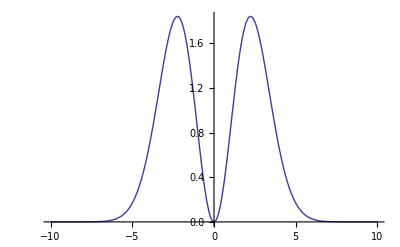

```mathematica
field[r_]:=r^2 ⅇ^(-r^2/5)
Plot[field[r], {r, -10, 10}]
```

```mathematica
surface[θ_, ϕ_]:=2.0*(1.0+(*0.3*Sin[θ]*(Cos[ϕ]+Sin[ϕ])+*)0.2*(1-Cos[2*θ])*(Cos[2*ϕ]+Sin[2*ϕ]))
SphericalPlot3D[surface[θ, ϕ], {θ,0,Pi},{ϕ,0,2Pi}, MaxRecursion->1]
```

-Graphics3D-

```mathematica
2.234633135269820325e+00 6.283185307179586232e-01 3.769911184307751739e+00 1.839395690773730774e+00 1.684486749771372804e-01-9.084217301247018428e-01
```

```mathematica
surface[6.283185307179586232*^-1, 3.769911184307751739*^0]
```

2.34828

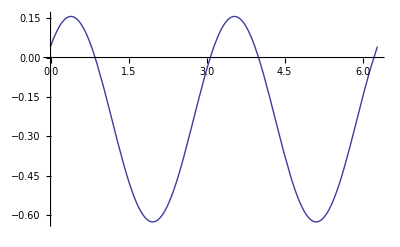

```mathematica
Plot[surface[6.283185307179586232*^-1, ϕ]-2.234633135269820325, {ϕ, 0, 2π}]
```

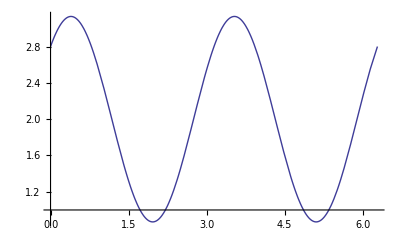

```mathematica
Plot[surface[π/2, ϕ], {ϕ, 0, 2π}]
```

```mathematica
N[π/2, 18]
```

1.57079632679489662

```mathematica
surface[1.570796, 1.88495559]
```

0.882558

```mathematica
NMinimize[{surface[π/2, ϕ], 1<ϕ<3}, ϕ]
```

{0.868629,{ϕ→1.9635}}

```mathematica
znew=0,i=26,j=10,k=5,zold=0,R0=2.668766,rnew=0.852640,theta=1.570796,phi=0.785398,f=0.628616)
```

```mathematica
surface[1.570796, 0.785398]
```

2.8